```mathematica
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"code","2D","out"}]]
```

/home/florian/Projects/university/masters_thesis/code/2D/out

```mathematica
values = {2,3,4,5,7,10,15,20,25,30,40};
```

```mathematica
loadCSV[collision_String,size_Integer]:=Delete[Import["schaeferTurek_"<>collision<>"_Re100_size"<>ToString[size],"CSV"],1];
getDragData[collision_String,size_Integer] := Drop[Map[Delete[#,3]&,loadCSV[collision,size]],1000];getLiftData[collision_String,size_Integer] := Drop[Map[Delete[#,2]&,loadCSV[collision,size]],1000];
getDragDataFrequency[collision_String, size_Integer] := Abs[Fourier[ #[[2]]&/@getDragData[collision,size]]];
getCumulantAndSRT[size_Integer] :={getDragData["cumulant",size],getDragData["srt", size]};
PlotCumulantVsSRT[size_Integer] := ListLinePlot[getCumulantAndSRT[size],PlotLegends->{"cumulant","SRT"}];
getCumulantAndNextSRT[position_Integer] := {getDragData["cumulant",values[[position]]],getDragData["srt", values[[position+1]]]};
PlotCumulantVsNextSRT[position_Integer] := ListLinePlot[getCumulantAndNextSRT[position],PlotLegends->{"cumulant","SRT"}];
getCumulantAndShiftSRT[position_Integer,shift_Integer] := {getDragData["cumulant",values[[position]]],getDragData["srt", values[[position+shift]]]};
PlotCumulantVsShiftSRT[position_Integer,shift_Integer] := ListLinePlot[getCumulantAndShiftSRT[position,shift],PlotLegends->{"cumulant","SRT"}];
getCumulantsFromTo[start_Integer,end_Integer] := getDragData["cumulant",values[[#]]]&/@Range[start,end];
plotCumulantsFromTo[start_Integer,end_Integer] := ListLinePlot[getCumulantsFromTo[start,end],PlotLegends->ToString /@ (values[[#]]&/@ Range[3,8])];getSRTFromTo[start_Integer,end_Integer] := getDragData["srt",values[[#]]]&/@Range[start,end];
plotSRTFromTo[start_Integer,end_Integer] := ListLinePlot[getSRTFromTo[start,end],PlotLegends->ToString /@ (values[[#]]&/@ Range[3,8])];
getCumulantsFrequencyFromTo[start_Integer,end_Integer] := getDragDataFrequency["cumulant",values[[#]]]&/@Range[start,end];
plotCumulantsFrequencyFromTo[start_Integer,end_Integer] := ListLinePlot[getCumulantsFrequencyFromTo[start,end],PlotLegends->ToString /@ (values[[#]]&/@ Range[3,8]), PlotRange->All];plotCumulantsFrequencyFromToClip[start_Integer,end_Integer,clip_Integer] := ListLinePlot[Take[#,clip]&/@getCumulantsFrequencyFromTo[start,end],PlotLegends->ToString /@ (values[[#]]&/@ Range[3,8]), PlotRange->All];getSRTFrequencyFromTo[start_Integer,end_Integer] := getDragDataFrequency["srt",values[[#]]]&/@Range[start,end];
plotSRTFrequencyFromTo[start_Integer,end_Integer] := ListLinePlot[getSRTFrequencyFromTo[start,end],PlotLegends->ToString /@ (values[[#]]&/@ Range[3,8]), PlotRange->All];
plotSRTFrequencyFromToClip[start_Integer,end_Integer,clip_Integer] := ListLinePlot[Take[#,clip]&/@getSRTFrequencyFromTo[start,end],PlotLegends->ToString /@ (values[[#]]&/@ Range[3,8]), PlotRange->All];
```

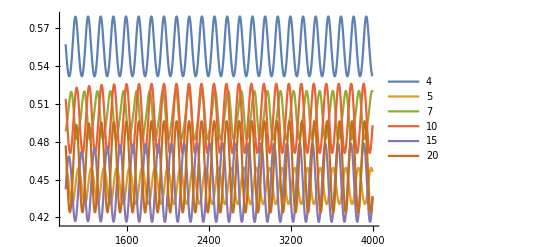

```mathematica
plotCumulantsFromTo[4,9]
```

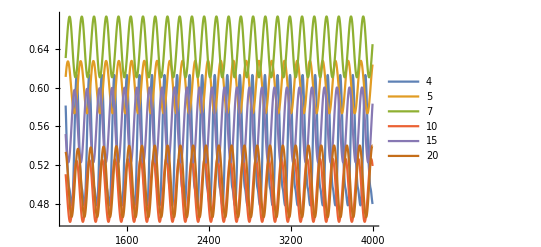

```mathematica
plotSRTFromTo[5,10]
```

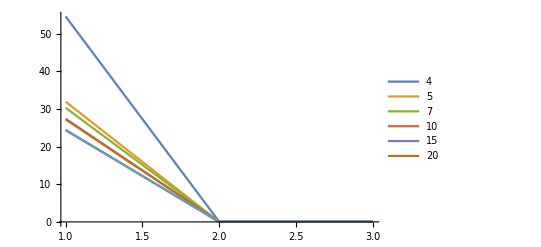

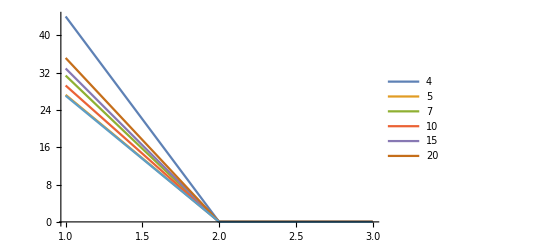

```mathematica
plotCumulantsFrequencyFromToClip[2,8,3]
plotSRTFrequencyFromToClip[2,8,3]
```